```mathematica
Some basic information;
```

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/NEB/FINAL_PATHS_FOR_PAPER/"];
file={"3_vol_temp_dist_energy"};
NEBdata=Table[ReadList[file[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}],{i,1,1}][[1]];
```

```mathematica
a={0.125,0,0.125};
b={0.1339,0.07524,0.3666};
c=b-a;
2Total[c^2]^0.5*2*4.6583+4.349635
2Total[c^2]^0.5*2*4.759+3.576795
2Total[c^2]^0.5*2*4.850+3.668868
```

9.06758

8.39673

8.58097

```mathematica
0.07924*4.6583*2
0.07924*4.759*2
0.07924*4.850*2
```

0.738247

0.754206

0.768628

```mathematica
}
```

```mathematica
NEBdata[[4]]
```

{3,4.6583,0,1.93139,0.995135,4.759,2479,2.29007,1.18229,4.85,3821,2.42791,1.4023}

```mathematica
-.67127382E+03
```

```mathematica
index=Transpose[NEBdata][[{1}]][[1]]
vols=Transpose[NEBdata][[{2,6,10}]]
temp=Transpose[NEBdata][[{3,7,11}]]
dist=Transpose[NEBdata][[{4,8,12}]]
e0s=Transpose[NEBdata][[{5,9,13}]]
```

{1,0,1,2,3,4,5,6}

{{4.6583,4.6583,4.6583,4.6583,4.6583,4.6583,4.6583,4.6583},{4.759,4.759,4.759,4.759,4.759,4.759,4.759,4.759},{4.85,4.85,4.85,4.85,4.85,4.85,4.85,4.85}}

{{0,0,0,0,0,0,0,0},{2479,2479,2479,2479,2479,2479,2479,2479},{3821,3821,3821,3821,3821,3821,3821,3821}}

{{-0.540279,0.,0.540279,0.881051,1.93139,4.34964,6.70861,9.06758},{-0.505926,0.,0.505926,0.917487,2.29007,3.5768,5.98676,8.39673},{-0.491838,0.,0.491838,0.973187,2.42791,3.66887,6.12492,8.58097}}

{{0.459286,0.,0.459286,0.390465,0.995135,-3.36282,5.,-3.36282},{0.415663,0.,0.415663,0.297066,1.18229,-2.82737,6.,-2.82737},{0.408561,0.,0.408561,0.224986,1.4023,-2.07754,7.,-2.07754}}

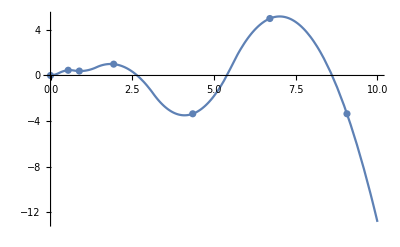

```mathematica
diste0s=Table[Transpose@{dist[[i]],e0s[[i]]},{i,1,3}];
ListLinePlot@diste0s;
Show[{Plot[Interpolation[diste0s[[1]],Method->"Spline",InterpolationOrder->2][x],{x,0,10}],ListPlot@diste0s[[1]]}]
```

```mathematica
Table[Partition[Flatten@Table[F[diste0s[[i]][[j]]*(1)^j],{j,1,Length[diste0s[[i]]]}],2],{i,1,3}]
```

{{{-0.540279,0.459286},{-0.530279,0.460286},{-0.550279,0.460286},{0.,0.},{0.01,0.001},{-0.01,0.001},{0.540279,0.459286},{0.550279,0.460286},{0.530279,0.460286},{0.881051,0.390465},{0.891051,0.391465},{0.871051,0.391465},{1.93139,0.995135},{1.94139,0.996135},{1.92139,0.996135},{4.34964,-3.36282},{4.35964,-3.36182},{4.33964,-3.36182},{6.70861,5.},{6.71861,5.001},{6.69861,5.001},{9.06758,-3.36282},{9.07758,-3.36182},{9.05758,-3.36182}},{{-0.505926,0.415663},{-0.495926,0.416663},{-0.515926,0.416663},{0.,0.},{0.01,0.001},{-0.01,0.001},{0.505926,0.415663},{0.515926,0.416663},{0.495926,0.416663},{0.917487,0.297066},{0.927487,0.298066},{0.907487,0.298066},{2.29007,1.18229},{2.30007,1.18329},{2.28007,1.18329},{3.5768,-2.82737},{3.5868,-2.82637},{3.5668,-2.82637},{5.98676,6.},{5.99676,6.001},{5.97676,6.001},{8.39673,-2.82737},{8.40673,-2.82637},{8.38673,-2.82637}},{{-0.491838,0.408561},{-0.481838,0.409561},{-0.501838,0.409561},{0.,0.},{0.01,0.001},{-0.01,0.001},{0.491838,0.408561},{0.501838,0.409561},{0.481838,0.409561},{0.973187,0.224986},{0.983187,0.225986},{0.963187,0.225986},{2.42791,1.4023},{2.43791,1.4033},{2.41791,1.4033},{3.66887,-2.07754},{3.67887,-2.07654},{3.65887,-2.07654},{6.12492,7.},{6.13492,7.001},{6.11492,7.001},{8.58097,-2.07754},{8.59097,-2.07654},{8.57097,-2.07654}}}

```mathematica
(*Function to force the gradients to be correct either side*)
deltaX=0.5;
deltaForce=0.00005
F[{a_,b_},j_]:={{a,b},{a+deltaX/1000,b+((-1)^(j))deltaForce},{a-deltaX/1000,b+((-1)^(j))deltaForce}}
diste0sGrad=Table[Partition[Flatten@Table[F[diste0s[[i]][[j]],j],{j,1,Length[diste0s[[i]]]}],2],{i,1,3}]
diste0sGradGP=Table[Flatten[{#1->#2}&@@@diste0sGrad[[i]]],{i,1,3}]
Pdiste0sGradGP=Table[Predict[diste0sGradGP[[i]],Method->"GaussianProcess"],{i,1,3}]
```

0.00005

{{{-0.540279,0.459286},{-0.539779,0.459236},{-0.540779,0.459236},{0.,0.},{0.0005,0.00005},{-0.0005,0.00005},{0.540279,0.459286},{0.540779,0.459236},{0.539779,0.459236},{0.881051,0.390465},{0.881551,0.390515},{0.880551,0.390515},{1.93139,0.995135},{1.93189,0.995085},{1.93089,0.995085},{4.34964,-3.36282},{4.35014,-3.36277},{4.34914,-3.36277},{6.70861,5.},{6.70911,4.99995},{6.70811,4.99995},{9.06758,-3.36282},{9.06808,-3.36277},{9.06708,-3.36277}},{{-0.505926,0.415663},{-0.505426,0.415613},{-0.506426,0.415613},{0.,0.},{0.0005,0.00005},{-0.0005,0.00005},{0.505926,0.415663},{0.506426,0.415613},{0.505426,0.415613},{0.917487,0.297066},{0.917987,0.297116},{0.916987,0.297116},{2.29007,1.18229},{2.29057,1.18224},{2.28957,1.18224},{3.5768,-2.82737},{3.5773,-2.82732},{3.5763,-2.82732},{5.98676,6.},{5.98726,5.99995},{5.98626,5.99995},{8.39673,-2.82737},{8.39723,-2.82732},{8.39623,-2.82732}},{{-0.491838,0.408561},{-0.491338,0.408511},{-0.492338,0.408511},{0.,0.},{0.0005,0.00005},{-0.0005,0.00005},{0.491838,0.408561},{0.492338,0.408511},{0.491338,0.408511},{0.973187,0.224986},{0.973687,0.225036},{0.972687,0.225036},{2.42791,1.4023},{2.42841,1.40225},{2.42741,1.40225},{3.66887,-2.07754},{3.66937,-2.07749},{3.66837,-2.07749},{6.12492,7.},{6.12542,6.99995},{6.12442,6.99995},{8.58097,-2.07754},{8.58147,-2.07749},{8.58047,-2.07749}}}

{{-0.540279→0.459286,-0.539779→0.459236,-0.540779→0.459236,0.→0.,0.0005→0.00005,-0.0005→0.00005,0.540279→0.459286,0.540779→0.459236,0.539779→0.459236,0.881051→0.390465,0.881551→0.390515,0.880551→0.390515,1.93139→0.995135,1.93189→0.995085,1.93089→0.995085,4.34964→-3.36282,4.35014→-3.36277,4.34914→-3.36277,6.70861→5.,6.70911→4.99995,6.70811→4.99995,9.06758→-3.36282,9.06808→-3.36277,9.06708→-3.36277},{-0.505926→0.415663,-0.505426→0.415613,-0.506426→0.415613,0.→0.,0.0005→0.00005,-0.0005→0.00005,0.505926→0.415663,0.506426→0.415613,0.505426→0.415613,0.917487→0.297066,0.917987→0.297116,0.916987→0.297116,2.29007→1.18229,2.29057→1.18224,2.28957→1.18224,3.5768→-2.82737,3.5773→-2.82732,3.5763→-2.82732,5.98676→6.,5.98726→5.99995,5.98626→5.99995,8.39673→-2.82737,8.39723→-2.82732,8.39623→-2.82732},{-0.491838→0.408561,-0.491338→0.408511,-0.492338→0.408511,0.→0.,0.0005→0.00005,-0.0005→0.00005,0.491838→0.408561,0.492338→0.408511,0.491338→0.408511,0.973187→0.224986,0.973687→0.225036,0.972687→0.225036,2.42791→1.4023,2.42841→1.40225,2.42741→1.40225,3.66887→-2.07754,3.66937→-2.07749,3.66837→-2.07749,6.12492→7.,6.12542→6.99995,6.12442→6.99995,8.58097→-2.07754,8.58147→-2.07749,8.58047→-2.07749}}

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

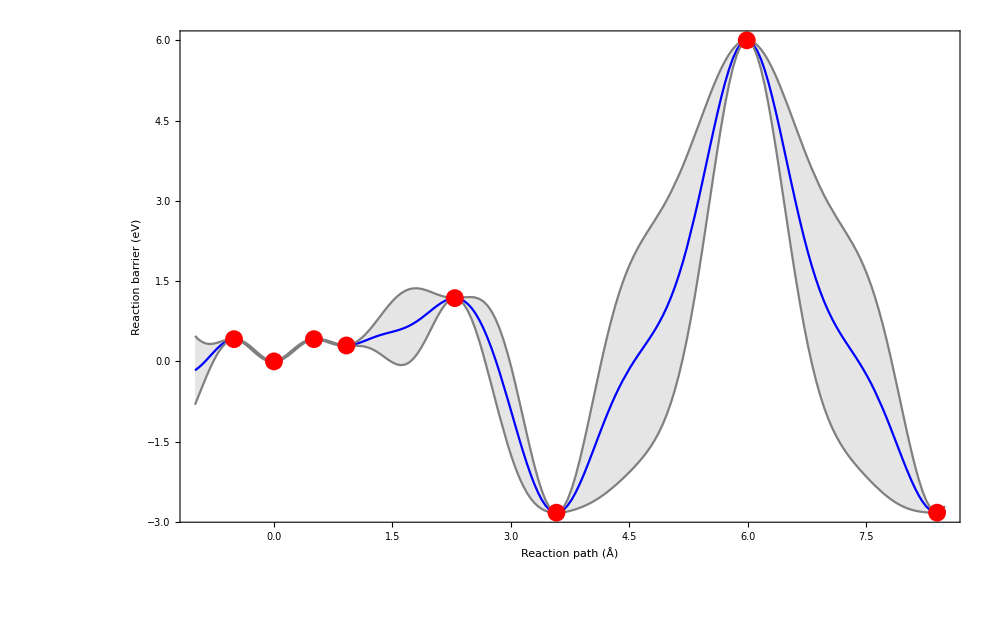

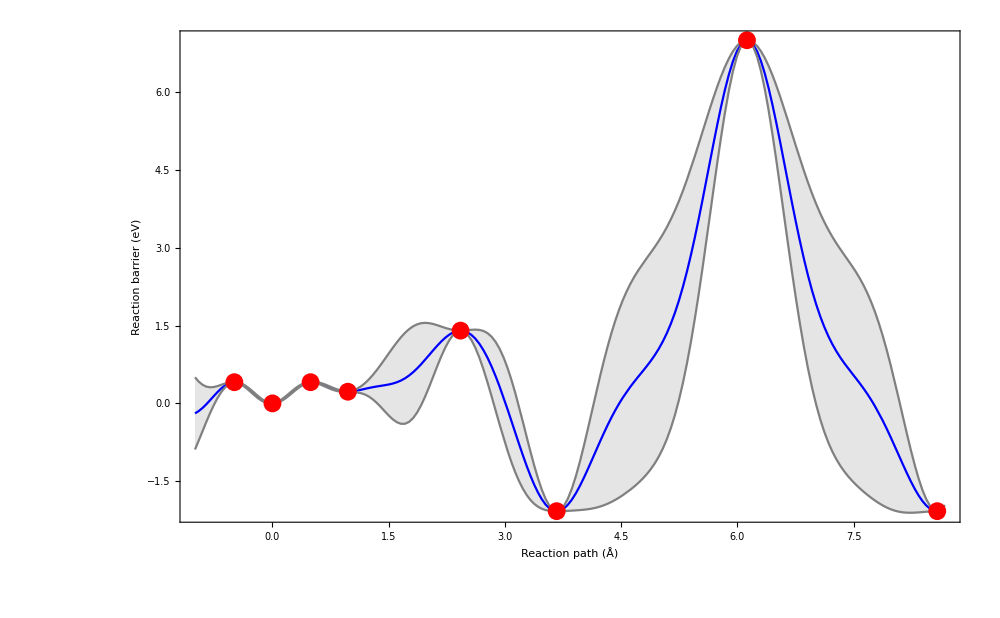

```mathematica
With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,-1,Evaluate[dist[[vol]][[-1]]]+0.1},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->1000],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,-1,Evaluate[dist[[vol]][[-1]]]+0.1},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->1000],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
```

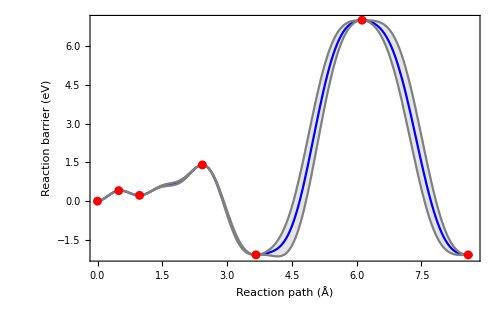

```mathematica
With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
```

```mathematica
legends={{"T=0 K turning-point data"},{"T=2500 K turning-point data"},{"T=3800 K turning-point data"}};
```

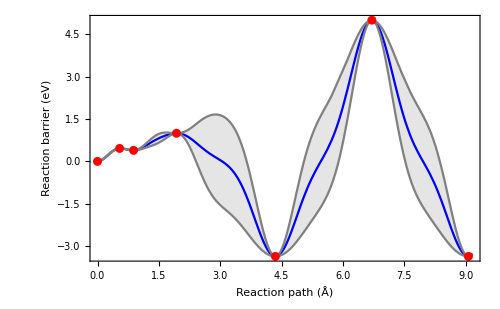

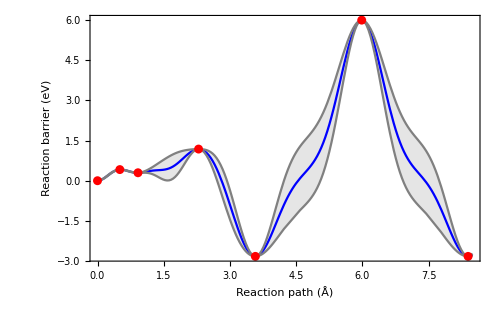

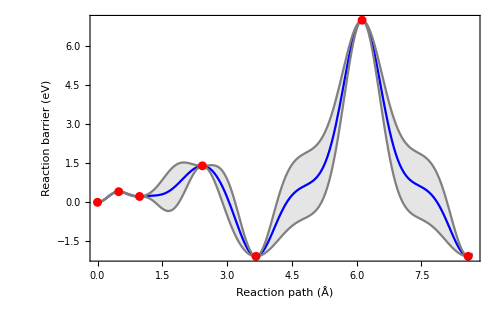

```mathematica
gp1=With[{vol=1},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[List@@@diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
gp2=With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
gp3=With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
```

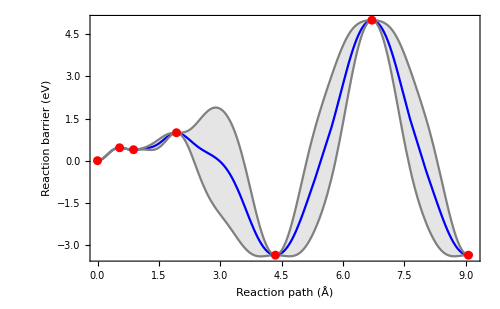

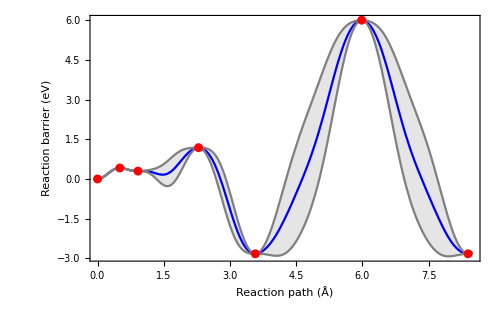

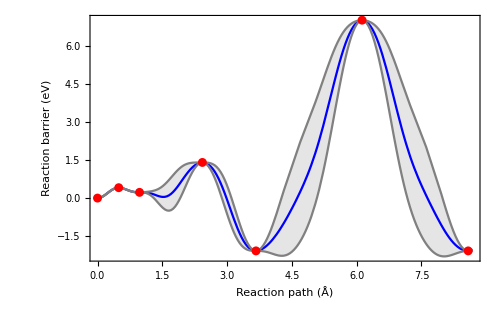

```mathematica
gp1=With[{vol=1},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[List@@@diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
gp2=With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
gp3=With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
```

```mathematica
e
```